```mathematica
repoDir=FileNameJoin[{$InitialDirectory,"Dropbox","Archives","GitHub","NuclideChart"}];
```

#### Animation

```mathematica
zmin=1;
zmax=45 (*26*);
factor=1.0;
amin=Min[IsotopeData[zmin,"MassNumber"]]-zmin*1;
amax=Max[IsotopeData[zmax,"MassNumber"]]-zmax*1;
g=Quiet@Table[IsotopeData[{z,a},"BindingEnergy"],{z,zmin,zmax},{a,amin,amax}];
MaxBindingEnergy=Max[Cases[Flatten[g],_Real]];
gInv=Quiet@Table[factor*(MaxBindingEnergy-IsotopeData[{z,a},"BindingEnergy"]),{z,zmin,zmax},{a,amin,amax}];
```

```mathematica
gr=Quiet@ListPlot3D[gInv,
InterpolationOrder->0,
Mesh->None,
BoxRatios->Automatic,
PlotRange->All,
AspectRatio->2,
Filling->Axis,
Ticks->None,
FillingStyle->Directive[LightGray,Opacity[0.50]],
PlotStyle->Directive[Opacity[0.75]],
ColorFunction->"Rainbow",
ImageSize->{1000,600},
PreserveImageOptions->False,
RotationAction->"Clip"
];
```

```mathematica
Animate[
With[{v=RotationTransform[θ,{0,0,1}][4.5*{1,0,0.2}]},
Column[{
Graphics3D[{Red,PointSize[Large],Point[v],Line[{v,{0,0,0}}],Black,PointSize[Large],Point[{0,0,0}]},PlotRange->2],
Show[gr,ViewPoint->v,ViewAngle->4.5°,RotationAction->"Clip"],
Dynamic[v]
}]],
{θ,0.25Pi,2.25Pi},
AnimationRunning->True]
```

```mathematica
oneFrame[θ_]:=Module[{v,a=4°,d=4.5},
v=RotationTransform[θ,{0,0,1}][d*{1,0,0.2}];
Show[Show[gr,ViewPoint->v,ViewAngle->a,RotationAction->"Clip"]]
];
```

```mathematica
oneFrame[-0.15Pi];
```

```mathematica
360/72.
```

5.

```mathematica
allFrame=Module[{nbFrame=72},
Table[oneFrame[(i/nbFrame)*2Pi],{i,nbFrame}]
];
```

```mathematica
name="rotatingNuclide3DChart";
Export[FileNameJoin[{repoDir,"Pictures",name<>".gif"}],allFrame,ImageSize->Automatic,"DisplayDurations"->0.1];
```

#### Graphs

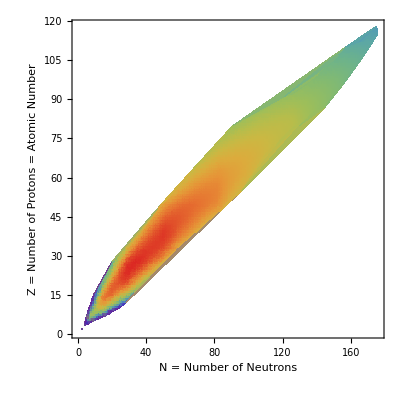

```mathematica
g1=Table[{a-z,z,IsotopeData[{z,a},"BindingEnergy"]},{z,1,118},{a,IsotopeData[z,"MassNumber"]}]//Flatten[#,1]&;
ListDensityPlot[g1,FrameLabel->{"N = Number of Neutrons","Z = Number of Protons = Atomic Number"},ColorFunction->"Rainbow"]
```

```mathematica
isotopeDataBindingEnergy[z_,a_]:=Module[{t},
t=Quiet@IsotopeData[{z,a},"BindingEnergy"];
If[NumericQ[t],t,0]
];
g2=Table[isotopeDataBindingEnergy[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
legend1=Rasterize@Graphics[Legend[ColorData["Rainbow"][1-#1]&,10,"High","Low",LegendShadow->None],ImageSize->50,ImagePadding->0]
```

-Graphics-

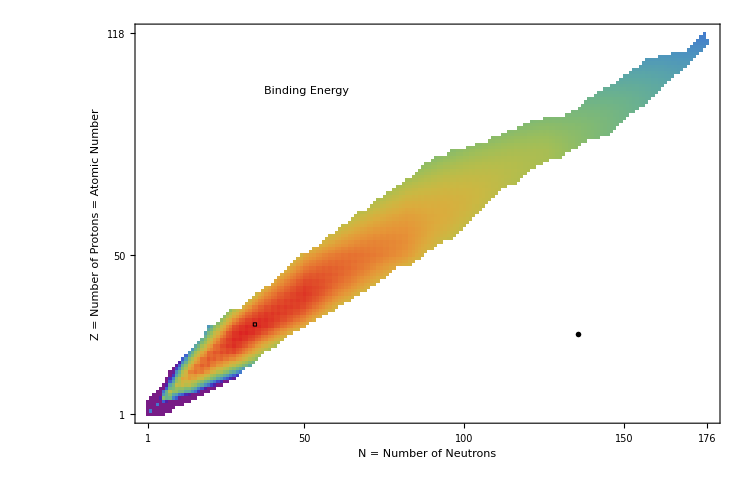

```mathematica
output=ArrayPlot[g2,DataReversed->True,ColorRules->{0->White},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{6.5,8.8},{0,1}]]&),AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{{EdgeForm[Black],Opacity[0],Rectangle[{34-0.5,28-0.5},{34+0.5,28+0.5}]},Inset[legend1,{135,25}],Inset[Text@Style["Binding Energy",Bold,20],{50,100}]}]
```

```mathematica
name="bindingEnergyNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
isotopeDataStable[z_,a_]:=Module[{t},
t=Quiet@IsotopeData[{z,a},"Stable"];
If[NumberQ[Boole[t]],Boole[t],-1]
];
g3=Table[isotopeDataStable[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
legendPlot[colorList_,labelList_]:=Module[{t},
t=Table[{Graphics[{colorList[[i]],Rectangle[{-1,-1},{1,1}]},ImageSize->15]," ",Text@Style[labelList[[i]],12,Bold]},{i,Length[colorList]}];
(*Framed[Column[Map[Row,t]]]*)
Column[Map[Row,t]]
];
```

```mathematica
colorList={Darker[Blue,0.7],Lighter[Blue,0.4]};
labelList={"Stable","Unstable"};
legend2=legendPlot[colorList,labelList]
```

-Graphics- Stable
-Graphics- Unstable

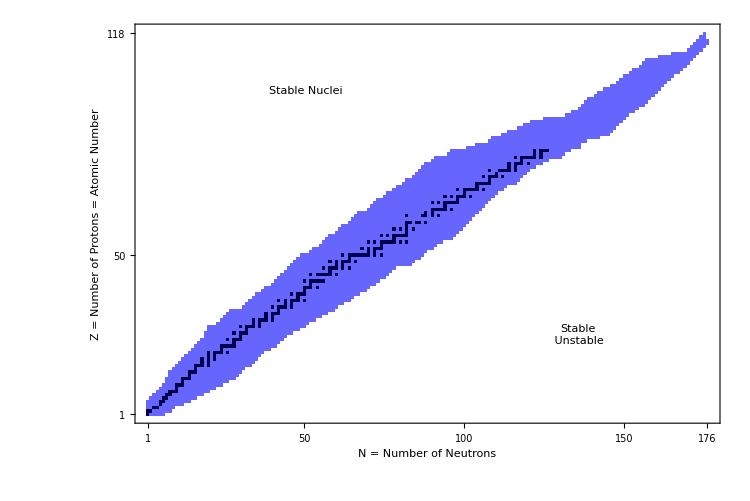

```mathematica
output=ArrayPlot[g3,DataReversed->True,ColorRules->{1->Darker[Blue,0.7],0->Lighter[Blue,0.4],-1->White},ColorFunction->"Rainbow",AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{Inset[legend2,{135,25}],Inset[Text@Style["Stable Nuclei",Bold,20],{50,100}]}]
```

```mathematica
name="stableNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
isotopeDataDecayModes[z_,a_]:=Module[{t,u,output},
t=Quiet@IsotopeData[{z,a},"DecayModes"];
u=Quiet@IsotopeData[{z,a},"Stable"];
If[!VectorQ[t],
output=-1,
If[Length[t]≥1,
output=Which[
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"BetaPlusDecay","BetaPlusDelayed"~~__,"ElectronCapture","DoubleBetaPlusDecay","PositronEmission"}],1,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{___~~"ProtonEmission"}],2,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"BetaDecay","BetaDelayed"~~__,"DoubleBetaDecay"}],3,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{___~~"NeutronEmission"}],4,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"AlphaEmission"}],5,
1==Max@Map[Boole@StringMatchQ[t[[1]],#]&,{"SpontaneousFission"}],6,
True,7
]
];
If[u==True,output=0]
];
output
];
g4=Table[isotopeDataDecayModes[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
colorList={Black,Lighter[Blue,0.5], Magenta,Orange,Red,Yellow,Green};
labelList={"Stable","β+","Proton Emission","β-","Neutron Emission","α","Spontaneous Fission"};
legend3=legendPlot[colorList,labelList]
```

-Graphics- Stable
-Graphics- β+
-Graphics- Proton Emission
-Graphics- β-
-Graphics- Neutron Emission
-Graphics- α
-Graphics- Spontaneous Fission

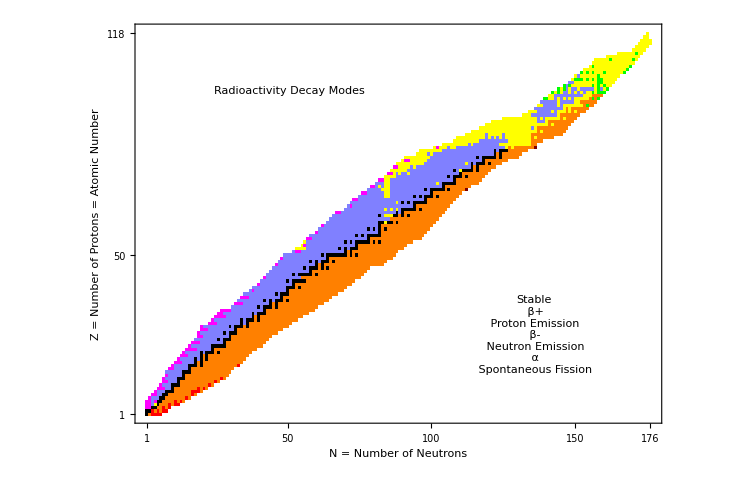

```mathematica
output=ArrayPlot[g4,DataReversed->True,ColorRules->{-1->White,0->Black,1->Lighter[Blue,0.5], 2->Magenta,3->Orange,4->Red,5->Yellow,6->Green,7->Gray},AspectRatio->Automatic,Frame->True,FrameTicks->All,ImageSize->750,Mesh->0,PixelConstrained->False,FrameLabel->(Text@Style[#,Bold,14]&)/@{"Z = Number of Protons = Atomic Number","N = Number of Neutrons"},Epilog->{Inset[legend3,{135,25}],Inset[Text@Style["Radioactivity Decay Modes",Bold,20],{50,100}]}]
```

```mathematica
name="radioactivityNuclide";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

```mathematica
(*is=Select[IsotopeData[],100≤IsotopeData[#,"MassNumber"]≤102&];
LayeredGraphPlot[Table[(IsotopeData[#,"FullSymbol"]&/@(i->#))&/@IsotopeData[i,"DaughterNuclides"],{i,is}]//Flatten,AspectRatio->0.75,DirectedEdges->True,VertexLabeling->True,ImageSize->700]*)
```

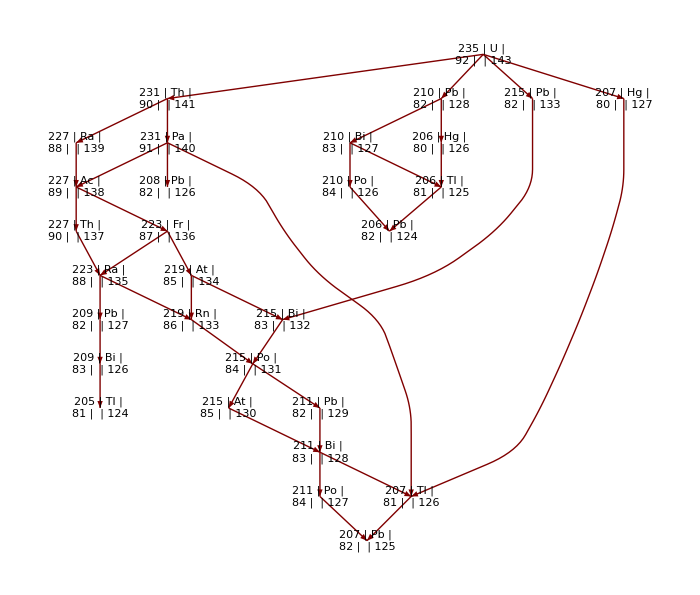

```mathematica
DaughterNuclides[s_List]:=DeleteCases[Union[Apply[Join,Map[IsotopeData[#,"DaughterNuclides"]&,DeleteCases[s,_Missing]]]],_Missing];
ReachableNuclides[s_List]:=FixedPoint[Union[Join[#,DaughterNuclides[#]]]&,s];
DecayNetwork[iso_List]:=Apply[Join,Map[Thread[#->DaughterNuclides[{#}]]&,ReachableNuclides[iso]]];
DecayNetworkPlot[s_]:=LayeredGraphPlot[Map[IsotopeData[#,"FullSymbol"]&,DecayNetwork[{s}],{2}],VertexLabeling->True,(*VertexRenderingFunction->(Text[Framed[Style[#2,8],Background->LightYellow],#1]&),*)ImageSize->{700,700},AspectRatio->0.85,DirectedEdges->True];

output=DecayNetworkPlot["Uranium235"]
```

```mathematica
name="u235DecayGraph";
Export[FileNameJoin[{repoDir,"Pictures",name<>".png"}],output,"PNG",ImageSize->Automatic];
```

#### Testing Zone

```mathematica
Max[Flatten[g2]]
```

8.794549

```mathematica
IsotopeData[28,"Name"]
IsotopeData[{28,62},"BindingEnergy"]
IsotopeData[{28,62},"Name"]
IsotopeData[{28,62},"FullSymbol"]
IsotopeData[{28,62},"Stable"]
```

{nickel-48,nickel-49,nickel-50,nickel-51,nickel-52,nickel-53,nickel-54,nickel-55,nickel-56,nickel-57,nickel-58,nickel-59,nickel-60,nickel-61,nickel-62,nickel-63,nickel-64,nickel-65,nickel-66,nickel-67,nickel-68,nickel-69,nickel-70,nickel-71,nickel-72,nickel-73,nickel-74,nickel-75,nickel-76,nickel-77,nickel-78}

8.794549

nickel-62

62 | Ni | 
28 |  | 34

True

```mathematica
Transpose[{IsotopeData[26,"NeutronNumber"],IsotopeData[26,"Stable"]}]
```

{{19,False},{20,False},{21,False},{22,False},{23,False},{24,False},{25,False},{26,False},{27,False},{28,True},{29,False},{30,True},{31,True},{32,True},{33,False},{34,False},{35,False},{36,False},{37,False},{38,False},{39,False},{40,False},{41,False},{42,False},{43,False},{44,False},{45,False},{46,False}}

```mathematica
IsotopeData[{2,4},"FullSymbol"]
IsotopeData[{2,4},"Name"]
```

4 | He | 
2 |  | 2

helium-4

```mathematica
nbDecayMode[z_,a_]:=Module[{t,output},
t=Quiet@IsotopeData[{z,a},"DecayModes"];
If[!VectorQ[t],Length[t],0]
];
```

```mathematica
nbDecayModePerIsotope=Table[nbDecayMode[z,z+n],{z,1,118},{n,Max[IsotopeData[z,"MassNumber"]]-z}];
```

```mathematica
N@Mean@Flatten@nbDecayModePerIsotope
```

1.45079

```mathematica
allDecayMode=SortBy[Tally[Flatten[Table[IsotopeData[z,"DecayModes"],{z,118}]]],Last];
Length[allDecayMode]
Total[allDecayMode[[All,2]]]
Total[allDecayMode[[25;;]][[All,2]]]
```

43

4490

4442

```mathematica
allDecayMode[[25;;]]
```

{{TwoNeutronEmission,8},{BetaPlusDelayedTwoProtonEmission,9},{BetaDelayedAlphaEmission,10},{PositronEmission,11},{BetaPlusDelayedFission,14},{TwoProtonEmission,16},{BetaDelayedTwoNeutronEmission,21},{NeutronEmission,24},{BetaPlusDelayedAlphaEmission,36},{DoubleBetaDecay,42},{DoubleBetaPlusDecay,46},{ProtonEmission,97},{ElectronCapture,147},{BetaPlusDelayedProtonEmission,200},{SpontaneousFission,203},{BetaDelayedNeutronEmission,316},{AlphaEmission,830},{BetaDecay,1190},{BetaPlusDecay,1222}}

```mathematica
IsotopeData["Classes"]
```

{AlphaEmission,BetaDecay,BetaDelayedAlphaEmission,BetaDelayedDeuteronEmission,BetaDelayedFission,BetaDelayedFourNeutronEmission,BetaDelayedNeutronAlphaEmission,BetaDelayedNeutronEmission,BetaDelayedThreeNeutronEmission,BetaDelayedTritonEmission,BetaDelayedTwoNeutronEmission,BetaPlusDecay,BetaPlusDelayedAlphaEmission,BetaPlusDelayedFission,BetaPlusDelayedProtonAlphaEmission,BetaPlusDelayedProtonEmission,BetaPlusDelayedThreeProtonEmission,BetaPlusDelayedTwoProtonEmission,Boson,Carbon12ClusterEmission,Carbon14ClusterEmission,DoubleBetaDecay,DoubleBetaPlusDecay,ElectronCapture,Fermion,Fluorine23ClusterEmission,Magnesium28ClusterEmission,Magnesium28Magnesium30ClusterEmission,Magnesium30ClusterEmission,Neon20ClusterEmission,Neon22ClusterEmission,Neon24ClusterEmission,Neon24Neon26ClusterEmission,Neon25ClusterEmission,NeutronEmission,Oxygen18ClusterEmission,Oxygen20ClusterEmission,PositronEmission,ProtonEmission,Silicon32ClusterEmission,Silicon34ClusterEmission,SpontaneousFission,Stable,ThreeNeutronEmission,TwoNeutronEmission,TwoProtonEmission,Unstable}

```mathematica
t=Table[Length[IsotopeData[z,"MassNumber"]],{z,118}]
```

{7,9,10,12,14,15,16,17,18,19,20,22,22,23,23,24,24,24,24,24,25,26,26,26,26,28,29,31,29,30,31,32,33,30,31,32,32,33,33,33,33,33,34,34,34,34,38,38,39,39,37,38,37,38,40,40,39,39,39,38,38,38,38,36,36,36,36,35,35,35,35,36,36,35,35,35,36,37,37,40,37,38,36,33,31,34,34,33,31,30,29,26,20,20,19,20,20,20,19,19,18,17,16,16,16,16,16,15,15,15,12,9,5,5,5,4,2,1}

```mathematica
t1=Table[{IsotopeData[z,"Name"],IsotopeData[z,"MassNumber"],IsotopeData[z,"AtomicNumber"],IsotopeData[z,"MassNumber"]-IsotopeData[z,"AtomicNumber"]},{z,113,118}]//Column
```

{{ununtrium-283,ununtrium-284,ununtrium-285,ununtrium-286,ununtrium-287},{283,284,285,286,287},{113,113,113,113,113},{170,171,172,173,174}}
{{ununquadium-285,ununquadium-286,ununquadium-287,ununquadium-288,ununquadium-289},{285,286,287,288,289},{114,114,114,114,114},{171,172,173,174,175}}
{{ununpentium-287,ununpentium-288,ununpentium-289,ununpentium-290,ununpentium-291},{287,288,289,290,291},{115,115,115,115,115},{172,173,174,175,176}}
{{ununhexium-289,ununhexium-290,ununhexium-291,ununhexium-292},{289,290,291,292},{116,116,116,116},{173,174,175,176}}
{{ununseptium-291,ununseptium-292},{291,292},{117,117},{174,175}}
{{ununoctium-293},{293},{118},{175}}

```mathematica
zmin=1;
zmax=118;
t2=Module[{t},
t=Table[If[NumberQ@Quiet@IsotopeData[{z,a},"MassNumber"],{z,a-z,a,IsotopeData[{z,a},"Name"],IsotopeData[{z,a},"FullSymbol"],IsotopeData[{z,a},"Stable"]},0],{z,zmin,zmax},{a,Min[IsotopeData[z,"MassNumber"]],Max[IsotopeData[z,"MassNumber"]]}];
t
];
```

```mathematica
t2[[27;;28]];
```

```mathematica
t3=Select[Flatten[t2,1],#[[6]]==True&];
Length[t3]
```

256

```mathematica
t3[[-5;;]]
```

{{81,124,205,thallium-205,205 | Tl | 
81 |  | 124,True},{82,122,204,lead-204,204 | Pb | 
82 |  | 122,True},{82,124,206,lead-206,206 | Pb | 
82 |  | 124,True},{82,125,207,lead-207,207 | Pb | 
82 |  | 125,True},{82,126,208,lead-208,208 | Pb | 
82 |  | 126,True}}